16.9107

0.517159

Piecewise[{{-0.114774 z, 0≤z≤0.517159}, {-0.0593566-0.0689953 (-0.517159+z), 0.517159≤z≤2.06864}, {-0.166401+0.0797207 (-2.06864+z), 2.06864≤z≤2.5858}, {-0.125173-0.0526457 (-2.5858+z), 2.5858≤z≤4.13728}, {-0.206852+0.00532997 (-4.13728+z), 4.13728≤z≤4.65443}, {-0.204095+0.00568966 (-4.65443+z), 4.65443≤z≤6.20591}, {-0.195268-0.0268133 (-6.20591+z), 6.20591≤z≤6.72307}, {-0.209135-0.0591856 (-6.72307+z), 6.72307≤z≤8.27455}, {-0.30096-0.0595125 (-8.27455+z), 8.27455≤z≤8.79171}, {-0.331737-0.000163496 (-8.79171+z), 8.79171≤z≤10.3432}, {-0.213278-0.132432 (-10.3432+z), 10.3432≤z≤10.8603}, {-0.400479+0.0154667 (-10.8603+z), 10.8603≤z≤12.4118}, {-0.376483+0.0561445 (-12.4118+z), 12.4118≤z≤12.929}, {-0.347447-0.0516647 (-12.929+z), 12.929≤z≤14.4805}, {-0.427604+0.0276635 (-14.4805+z), 14.4805≤z≤14.9976}, {-0.413298-0.0130797 (-14.9976+z), 14.9976≤z≤16.5491}, {-0.43359-0.150089 (-16.5491+z), 16.5491≤z≤17.0663}, {-0.51121+0.168008 (-17.0663+z), 17.0663≤z≤18.6177}, {-0.250549-2.05187 (-18.6177+z), 18.6177≤z≤19.1349}, {-1.3117+2.98704 (-19.1349+z), 19.1349≤z≤20.6864}, {3.32263-11.413 (-20.6864+z), 20.6864≤z≤21.2035}, {-2.57971+4.93902 (-21.2035+z), 21.2035≤z≤22.755}, {5.08307-3.32682 (-22.755+z), 22.755≤z≤23.2722}, {3.36257+0.161207 (-23.2722+z), 23.2722≤z≤24.8237}, {3.61268-0.0961357 (-24.8237+z), 24.8237≤z≤25.3408}, {3.56297-0.0300833 (-25.3408+z), 25.3408≤z≤26.8923}, {3.51629-0.0618015 (-26.8923+z), 26.8923≤z≤27.4094}, {3.48433-0.00307372 (-27.4094+z), 27.4094≤z≤28.9609}, {3.47956-0.132759 (-28.9609+z), 28.9609≤z≤29.4781}, {3.41091+0.0155648 (-29.4781+z), 29.4781≤z≤31.0296}, {3.43505+0.0563734 (-31.0296+z), 31.0296≤z≤31.5467}, {3.46421-0.0519917 (-31.5467+z), 31.5467≤z≤33.0982}, {3.38354+0.0282848 (-33.0982+z), 33.0982≤z≤33.6154}, {3.39817-0.0255054 (-33.6154+z), 33.6154≤z≤35.1668}, {3.3586-0.0843639 (-35.1668+z), 35.1668≤z≤35.684}, {3.31497, 35.684≤z}, {0, True}}]

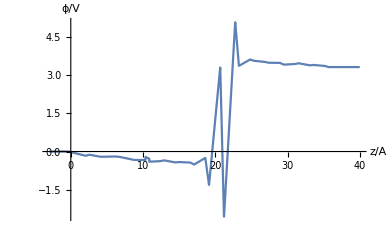

```mathematica
a=16.9107
c=0.01389*37.2325
Piecewise[{{-a*0.00351*z/c,0≤z≤c},{-a*0.00351-a*0.00211
*((z-c)/c),c≤z≤4*c},{-a*0.00351-a*0.00211
*3+a*0.002438
*((z-4*c)/c),4*c≤z≤5*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*((z-5*c)/c),5*c≤z≤8*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
*((z-8*c)/c),8*c≤z≤9*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*((z-9*c)/c),9*c≤z≤12*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
*((z-12*c)/c),12*c≤z≤13*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*((z-13*c)/c),13*c≤z≤16*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
*((z-16*c)/c),16*c≤z≤17*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*((z-17*c)/c),17*c≤z≤20*c},{a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
*((z-20*c)/c),20*c≤z≤21*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*((z-21*c)/c),21*c≤z≤24*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
*((z-24*c)/c),24*c≤z≤25*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*((z-25*c)/c),25*c≤z≤28*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
*((z-28*c)/c),28*c≤z≤29*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*((z-29*c)/c),29*c≤z≤32*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
*((z-32*c)/c),32*c≤z≤33*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*((z-33*c)/c),33*c≤z≤36*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
*((z-36*c)/c),36*c≤z≤37*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*((z-37*c)/c),37*c≤z≤40*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903*((z-40*c)/c),40*c≤z≤41*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*((z-41*c)/c),41*c≤z≤44*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
*((z-44*c)/c),44*c≤z≤45*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
+a*0.00493
*((z-45*c)/c),45*c≤z≤48*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
+a*0.00493
*3-a*0.00294
*((z-48*c)/c),48*c≤z≤49*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
+a*0.00493
*3-a*0.00294
-a*0.00092
*((z-49*c)/c),49*c≤z≤52*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
+a*0.00493
*3-a*0.00294
-a*0.00092
*3-a*0.00189
*((z-52*c)/c),52*c≤z≤53*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
+a*0.00493
*3-a*0.00294
-a*0.00092
*3-a*0.00189
-a*0.000094
*((z-53*c)/c),53*c≤z≤56*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
+a*0.00493
*3-a*0.00294
-a*0.00092
*3-a*0.00189
-a*0.000094
*3-a*0.00406
*((z-56*c)/c),56*c≤z≤57*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
+a*0.00493
*3-a*0.00294
-a*0.00092
*3-a*0.00189
-a*0.000094
*3-a*0.00406
+a*0.000476
*((z-57*c)/c),57*c≤z≤60*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
+a*0.00493
*3-a*0.00294
-a*0.00092
*3-a*0.00189
-a*0.000094
*3-a*0.00406
+a*0.000476
*3+a*0.001724
*((z-60*c)/c),60*c≤z≤61*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
+a*0.00493
*3-a*0.00294
-a*0.00092
*3-a*0.00189
-a*0.000094
*3-a*0.00406
+a*0.000476
*3+a*0.001724
-a*0.00159
*((z-61*c)/c),61*c≤z≤64*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
+a*0.00493
*3-a*0.00294
-a*0.00092
*3-a*0.00189
-a*0.000094
*3-a*0.00406
+a*0.000476
*3+a*0.001724
-a*0.00159
*3+a*0.000865
*((z-64*c)/c),64*c≤z≤65*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
+a*0.00493
*3-a*0.00294
-a*0.00092
*3-a*0.00189
-a*0.000094
*3-a*0.00406
+a*0.000476
*3+a*0.001724
-a*0.00159
*3+a*0.000865
-a*0.00078
*((z-65*c)/c),65*c≤z≤68*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
+a*0.00493
*3-a*0.00294
-a*0.00092
*3-a*0.00189
-a*0.000094
*3-a*0.00406
+a*0.000476
*3+a*0.001724
-a*0.00159
*3+a*0.000865
-a*0.00078
*3-a*0.00258
*((z-68*c)/c),68*c≤z≤69*c},{-a*0.00351-a*0.00211
*3+a*0.002438
-a*0.00161
*3+a*0.000163
+a*0.000174
*3-a*0.00082
-a*0.00181
*3-a*0.00182
-a*0.000005
*3-a*0.00405
+a*0.000473
*3+a*0.001717
-a*0.00158
*3+a*0.000846
-a*0.0004
*3-a*0.00459
+a*0.005138
*3-a*0.06275
+a*0.091349
*3-a*0.34903+a*0.151044
*3-a*0.10174
+a*0.00493
*3-a*0.00294
-a*0.00092
*3-a*0.00189
-a*0.000094
*3-a*0.00406
+a*0.000476
*3+a*0.001724
-a*0.00159
*3+a*0.000865
-a*0.00078
*3-a*0.00258
,69*c≤z}}]
Plot[%,{z,-3,40},AxesLabel->{"z/A","ϕ/V"}]
```